# Numerical Methods - Problem Set 6

## Problem 1

```mathematica
R00 = 2/3 h (f[0]+4 f[2]+f[4])
```

2/3 h (f[0]+4 f[2]+f[4])

```mathematica
R10 = Sum[(h/3)(f[2 i - 2] + 4 f[2 i - 1] + f[2 i]),{i, 1, 4/2}]
```

1/3 h (f[0]+4 f[1]+f[2])+1/3 h (f[2]+4 f[3]+f[4])

```mathematica
Simplify[R10]
```

1/3 h (f[0]+4 f[1]+2 f[2]+4 f[3]+f[4])

```mathematica
R11 = R10 + 1/15(R10 - R00)
```

1/3 h (f[0]+4 f[1]+f[2])+1/3 h (f[2]+4 f[3]+f[4])+1/15 (1/3 h (f[0]+4 f[1]+f[2])-2/3 h (f[0]+4 f[2]+f[4])+1/3 h (f[2]+4 f[3]+f[4]))

```mathematica
Simplify[R11]
```

2/45 h (7 f[0]+32 f[1]+12 f[2]+32 f[3]+7 f[4])

```mathematica
R11 = (16 R10 - R00)/15
```

1/15 (-2/3 h (f[0]+4 f[2]+f[4])+16 (1/3 h (f[0]+4 f[1]+f[2])+1/3 h (f[2]+4 f[3]+f[4])))

```mathematica
Simplify[R11]
```

2/45 h (7 f[0]+32 f[1]+12 f[2]+32 f[3]+7 f[4])

## Problem 2

```mathematica
f[x_]:= (2^x Sin[x])/x
```

```mathematica
xi = 0.1
xf = 1.1
```

0.1

1.1

```mathematica
Integrate[f[x],{x,xi,xf}]
```

1.41892

```mathematica
NumberForm[1.41891918440222,16]
```

1.41891918440222

```mathematica
Integrate[f[x],{x,-2,2}]
```

-π+1/2 ⅈ (ExpIntegralEi[-2 (ⅈ+Log[2])]-ExpIntegralEi[2 ⅈ-Log[4]]+ExpIntegralEi[-2 ⅈ+Log[4]]-ExpIntegralEi[2 ⅈ+Log[4]])

```mathematica
N[-π+1/2 ⅈ (ExpIntegralEi[-2 (ⅈ+Log[2])]-ExpIntegralEi[2 ⅈ-Log[4]]+ExpIntegralEi[-2 ⅈ+Log[4]]-ExpIntegralEi[2 ⅈ+Log[4]])]
```

4.12374+0. ⅈ

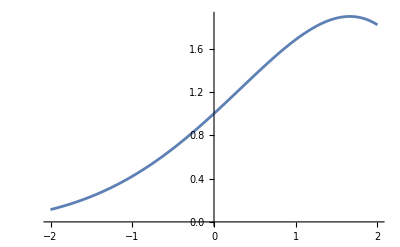

```mathematica
Plot[f[x],{x,-2,2}]
```

## a) Simpson’s 1/3 rule

```mathematica
intervals = 2
stepSize = (xf - xi)/intervals
```

2

0.5

```mathematica
xVals = {xi, xi+stepSize, xi + 2 * stepSize}
```

{0.1,0.6,1.1}

```mathematica
integralSimp = stepSize/3(f[xVals[[1]]] + 4 f[xVals[[2]]] + f[xVals[[3]]])
```

1.41871

## b) Simpson’s 1/3 rule with the Rhomberg algorithm

```mathematica
intervals = 4
stepSize = (xf - xi)/intervals
```

4

0.25

```mathematica
xVals = {xi, xi+stepSize, xi + 2 * stepSize, xi + 3 * stepSize, xi + 4 * stepSize}
```

{0.1,0.35,0.6,0.85,1.1}

```mathematica
integralRhomb = (2 stepSize)/45(7 f[xVals[[1]]] + 32 f[xVals[[2]]] + 12 f[xVals[[3]]] + 32 f[xVals[[4]]] + 7 f[xVals[[5]]])
```

1.41892

## c)

```mathematica
c = -1
d = 1
```

-1

1

```mathematica
a = 0.1
b = 1.1
```

0.1

1.1

-1

1

```mathematica
lambda = ((b-a)/(d-c))t + ((a d - b c)/(d - c))
```

(a+b)/2+1/2 (-a+b) t

```mathematica
dx = (b - a)/(d - c) dt
```

1/2 (-a+b) dt

```mathematica
xVals = {−0.861136, −0.339981, 0.339981,0.861136}
Aweights = {0.347855,0.652145, 0.652145 ,0.347855}
```

{-0.861136,-0.339981,0.339981,0.861136}

{0.347855,0.652145,0.652145,0.347855}

```mathematica
integral = 0.5 Sum[Aweights[[i]] f[0.5 xVals[[i]] + 0.6],{i,1,4}]
```

1.41892

```mathematica
NumberForm[integral,16]
```

1.418919186956585

## Problem 3

## a)

```mathematica
a = 0
b = 1
c = 0 
d = 2
```

0

1

0

2

```mathematica
f[x_,y_]:= x y^2
```

```mathematica
Integrate[f[x,y],{x,c,d},{y,a,b}]
```

2/3

```mathematica
hx = (d - c)/2
hy = (b - a)/2
xv = {c, c + hx, c + 2 hx}
yv = {a, a + hy, a + 2hy }
```

1

1/2

{0,1,2}

{0,1/2,1}

```mathematica
integ1 = ((d - c)(b-a))/36((f[xv[[1]],yv[[1]] ]+ 4 f[xv[[2]],yv[[1]] ] + f[xv[[3]],yv[[1]] ])
+ 4 (f[xv[[1]],yv[[2]] ] + 4 f[xv[[2]],yv[[2]] ] + f[xv[[3]],yv[[2]] ])
+ (f[xv[[1]],yv[[3]] ] + 4 f[xv[[2]],yv[[3]] ] + f[xv[[3]],yv[[3]] ]))
```

2/3

## b)

```mathematica
f[x_,y_]:= x y^2
```

```mathematica
a = 0
b = 1
c = 2 y
d = 2
```

0

1

2 y

2

```mathematica
hx[y_]:=(d - 2 y)/2
hy = (b - a)/2
xv[y_]:={2y, 2y + hx[y], d}
yv = {a, a + hy, a + 2hy }
```

1/2

{0,1/2,1}

```mathematica
integ2 = hy/9 *
(* y0 *)(hx[yv[[1]]] 
       (f[xv[yv[[1]]][[1]],yv[[1]] ]+ 
4 f[xv[yv[[1]]][[2]],yv[[1]] ] + 
    f[xv[yv[[1]]][[3]],yv[[1]] ])
+ 
(* y1 *)4 hx[yv[[2]]]
       (f[xv[yv[[2]]][[1]],yv[[2]] ] + 
4 f[xv[yv[[2]]][[2]],yv[[2]] ] + 
    f[xv[yv[[2]]][[3]],yv[[2]] ])
+ 
(* y2 *)hx[yv[[3]]]
       (f[xv[yv[[3]]][[1]],yv[[3]] ] + 
4 f[xv[yv[[3]]][[2]],yv[[3]] ] + 
    f[xv[yv[[3]]][[3]],yv[[3]] ]))
```

1/4

```mathematica
hx[yv[[1]]]
hx[yv[[2]]]
hx[yv[[3]]]
xv[yv[[1]]]
xv[yv[[2]]]
xv[yv[[3]]]
```

1

1/2

0

{0,1,2}

{1,3/2,2}

{2,2,2}